# Z-Scan Simulation using Gaussian Beam Propagation

## Overview

This notebook presents a numerical simulation of the Z-scan technique, based on Gaussian beam propagation through a Kerr nonlinear medium and implemented using ray-transfer (ABCD) matrix analysis.

## 1. Physical constants and parameters

This section defines all physical, optical, and numerical parameters used in the Z-scan simulation.

```mathematica
ClearAll["Global`*"];
```

```mathematica
(*=======Beam and laser parameters=======*)
λ=800*10^-9 ;           (*Wavelength[m]*)
ω0=0.4*10^-3;        (*Initial beam waist[m]*)
p=100*10^3;            (*Laser power[W]*)


(*=======Optical system parameters=======*)
f=0.13 ;                         (*Lens focal length[m]*)
d=1*10^-3;                 (*Kerr medium thickness[m]*)
n0=1.76;                        (*Linear refractive index*)
n2=3*10^-20;  (*3*10^-3;             Nonlinear refractive index[m^2/W]*)
L1 = 0.001;                        (*Distance between laser and lens ~ 0 *)


(*=======Scan parameters=======*)
z0=-0.05;                     (*Initial z position[m]*)
zf=0.05;                        (*Final z position[m]*)
nSteps=200;                 (*Number of scan points*)


(*=======Detector parameters=======*)
Rdet=0.5*ω0;           (*Aperture radius[m]*)


(*=======Derived quantities=======*)
I0[w_]:=2 p/(π w^2);  (*Peak intensity*)
q0=-I π ω0^2 n0/λ       (*Initial complex beam parameter*)
```

0.-1.10584 ⅈ

## 2. ABCD matrices

```mathematica
FreeSpace[L_]:={{1,L},{0,1}};

ThinLens[f_]:={{1,0},{-1/f,1}};

Interface[n1_,n2_]:={{1,0},{0,n1/n2}};

KerrLens[z_,w_]:=Module[{hk2},hk2=(8n2 p)/(n0 π w^4);
{{1,d},{-hk2 d,1}}];
```

## 3. Gaussian beam propagation utilities

```mathematica
qPropagate[q_,M_]:=(M[[1,1]] q+M[[1,2]])/(M[[2,1]] q+M[[2,2]]);

BeamWaist[q_]:=Sqrt[λ/(π n0 *Im[1/q])];
```

## 4. Power through aperture

```mathematica
DetectedPower[w_]:=p (1-Exp[-2 Rdet^2/w^2]);
```

## 5. Test case: single thin lens

```mathematica
LensOnly[z_]:=Module[{M,qf},M=FreeSpace[f+z].ThinLens[f].FreeSpace[f];
qf=qPropagate[q0,M];
BeamWaist[qf]];
```

```mathematica
zVals=Subdivide[z0,zf,nSteps];
waistLens=LensOnly/@zVals;
```

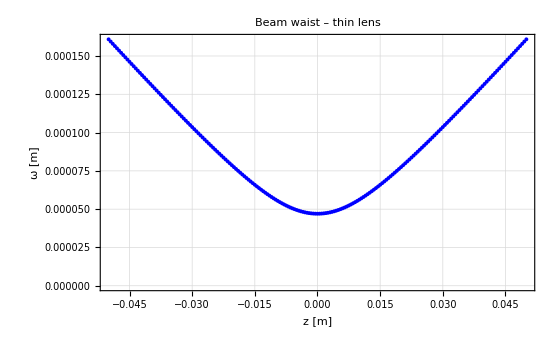

```mathematica
ListPlot[Transpose[{zVals,waistLens}],FrameLabel->{"z [m]","ω [m]"},PlotStyle->{PointSize[0.005],Blue},PlotLabel->"Beam waist – thin lens",GridLines->Automatic,Frame->True]
```

## 6. Z-scan simulation with Kerr medium

```mathematica
ZScan[z_]:=Module[{Mpre,qIn,wIn,hk2,Mkerr,Mtot,qDet,wDet},
(*Propagation up to the Kerr medium*)
Mpre=Interface[1,n0].FreeSpace[f+z].ThinLens[f].FreeSpace[L1];
qIn=qPropagate[q0,Mpre];
wIn=BeamWaist[qIn];
hk2=(n2*8*p ) /(n0*π*wIn^4);  (*Kerr parameter evaluated INSIDE the medium*)
Mkerr={{1,d},{-d*hk2 ,1}};

(*Full propagation to detector*)
Mtot=FreeSpace[f-z].Interface[n0,1].Mkerr.Mpre;
qDet=qPropagate[q0,Mtot];
wDet=BeamWaist[qDet];
{wDet,DetectedPower[wDet]}

];
```

```mathematica
zVals=Subdivide[z0,zf,nSteps];
zData=ZScan/@zVals;

waistZ=zData[[All,1]];
powerZ=zData[[All,2]];
```

## 7. Plots

```mathematica
waistZ;
```

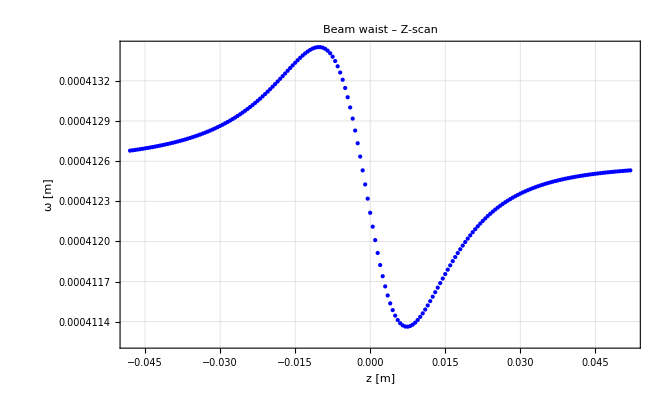

```mathematica
ListPlot[Transpose[{zVals+2*d,waistZ}],FrameLabel->{"z [m]","ω [m]"},PlotStyle->{PointSize[0.0045],Blue},GridLines->Automatic,Frame->True,PlotLabel->"Beam waist – Z-scan"]
```

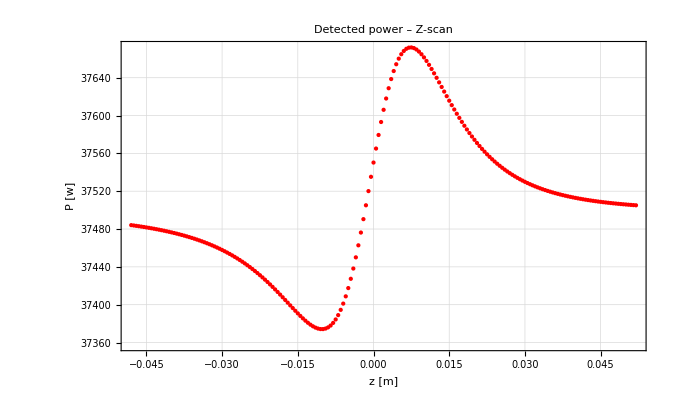

```mathematica
ListPlot[Transpose[{zVals+2d,powerZ}],FrameLabel->{"z [m]","P [w]"},PlotStyle->{PointSize[0.0045],Red},GridLines->Automatic,Frame->True,PlotLabel->"Detected power – Z-scan"]
```